# Hematopoietic Feedback

```mathematica
{Subscript[rH, 0],ρ,ϵ}/.ruleRH0ToRHSC/.ruleϵηρToAmpsParams[3,ruleParams]/.ruleParams
```

ReplaceAll::reps: {ruleRH0ToRHSC} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ruleϵηρToAmpsParams[3,ruleParams]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ruleParams} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{rH_0,ρ,ϵ}/.ruleRH0ToRHSC/.ruleϵηρToAmpsParams[3,ruleParams]/.ruleParams

```mathematica
αvRel[c_,j_,αs_]:=c/(ρ^j Subscript[rH, 0](1-ϵ))+ϵ/(1-ϵ)αs
```

## Parameter Fitting

```mathematica
ruleParams={ ϵHSC-> 1/2,rHSC-> 1/365,rMature-> 5,nHSC-> 400,μbs-> 1/100, bmOut-> 3.5*10^11};
ruleFluxjToRates={Subscript[λ, j_]-> 2 Subscript[sH, j],Subscript[μ, j_]-> Subscript[sH, j]-Subscript[vH, j]};
ruleμ0ToRates={Subscript[μ, 0]-> 0};
ruleNH0ToNHSC={Subscript[nH, 0]->nHSC/(2ϵ)};
ruleRH0ToRHSC={Subscript[rH, 0]->rHSC};
(*ruleRH1ToRHSC={Subscript[rH, 1]->rHSC ρ};*) 
(*ruleRates0ToRatesHSC={Subscript[vH, 0]-> Subscript[vH, HSC],Subscript[sH, 0]-> Subscript[sH, HSC]}*)
ruleRatesToRρϵ={Subscript[sH, 0]-> rHSC /2 ,Subscript[vH, 0]-> rHSC/2,Subscript[sH, j_]->Subscript[sH, 1] ρ^(j-1) ,Subscript[vH, j_]->Subscript[vH, 1] ρ^(j-1)}/.{Subscript[sH, 1]-> rHSC ϵ ρ,Subscript[vH, 1]->rHSC(1-ϵ)ρ}
ruleCompsizesToηϵ={Subscript[nH, j_]->Subscript[nH, 0] η^(j)}/.ruleNH0ToNHSC
Subscript[sH, 0] + Subscript[sH, 4]/.ruleRatesToRρϵ
```

{sH_0→rHSC/2,vH_0→rHSC/2,sH_j_→rHSC ϵ ρ^j,vH_j_→rHSC (1-ϵ) ρ^j}

{nH_j_→(nHSC η^j)/(2 ϵ)}

rHSC/2+rHSC ϵ ρ^4

```mathematica
ruleϵηρToAmpsParams[nAmps_,rParams_]:=
Quiet[
 Solve[
{
rHk==Subscript[rH, 0] ρ^nAmps,
nHk==Subscript[nH, 0] η^nAmps,
2ϵ rHk nHk==β,
η ρ == 2ϵ/(2ϵ-1),
 ϵ>0,ρ>1,η>1
}/.ruleRH0ToRHSC/.ruleNH0ToNHSC/.{rHk-> rMature,β-> bmOut}/.rParams
][[1]]
];
ruleCompsizeBloodToAmps[nAmps_]:={nHbs->2 Subscript[sH, nAmps] Subscript[nH, nAmps]/μbs}
ruleϵηρToAmpsParams[28,ruleParams]
```

{nHk→4.28212×10^10,ϵ→0.817352,η→1.96967,ρ→1.3076}

```mathematica
Subscript[nH, n]/.ruleCompsizesToηϵ/.ruleϵηρToAmpsParams[5, ruleParams]
```

0.994998 44.5254^n nHSC

```mathematica
Subscript[nH, 1]/.ruleCompsizesToηϵ/.ruleϵηρToAmpsParams[27,ruleParams]
Subscript[nH, 28]/.ruleCompsizesToηϵ/.ruleϵηρToAmpsParams[28,ruleParams]/.ruleParams
```

1.26255 nHSC

4.28212×10^10

What are our homeostatic values?

```mathematica
Subscript[sH, 1]/.ruleRatesToRρϵ/.ruleParams
Subscript[sH, 1]/.ruleRatesToRρϵ/.ruleParams/.ruleϵηρToAmpsParams[28,ruleParams]

Subscript[vH, 1]/.ruleRatesToRρϵ/.ruleParams
Subscript[vH, 1]/.ruleRatesToRρϵ/.ruleParams/.ruleϵηρToAmpsParams[28,ruleParams]
```

(ϵ ρ)/365

0.00292813

1/365 (1-ϵ) ρ

0.000654328

## Feedback types

Linear Feedback:

```mathematica
Module[
{f,fLin},
Manipulate[
f[ν_,α_]:=1-α*ν;
fLin[ν_,α_,κ_]:=
Piecewise[{{f[ν,α],0<f[ν,α]<κ},{0,0>f[ν,α]},{κ,f[ν,α]>κ}}];
Plot[fLin[ν,α,κ],{ν,-1,1},PlotRange->{-0.5,12}]
,
{{α,14},1,20},
{{κ,10},2,20}
]
]
```

### Linear feedback

```mathematica
sTLin[ν_,j_,κ_,α_]:=Subscript[sH, j](1-α*ν);
vTLin[ν_,j_,κ_,α_]:=Subscript[vH, j](1-α*ν);

sTLinStep[ν_,j_,κ_,α_]:=
Piecewise[{{Subscript[sH, j](1-α*ν),0≤1-α*ν≤κ},{0,0>1-α*ν},{κ Subscript[sH, j],1-α*ν>κ}}];
vTLinStep[ν_,j_,κ_,α_]:=
Piecewise[{{Subscript[vH, j](1-α*ν),0≤1-α*ν≤κ},{0,0>1-α*ν},{κ Subscript[vH, j],1-α*ν>κ}}];
```

### Logistic feedback:

```mathematica
fGLogistic[ν_,ν0_,k_,β_,ζ_]:=k-k*(1+Exp[-β(ν-ν0)])^(-1/ζ)

fGLogistic[ν,ν0,k,β,ζ]
```

k-(1+ⅇ^(-β (ν-ν0)))^(-1/ζ) k

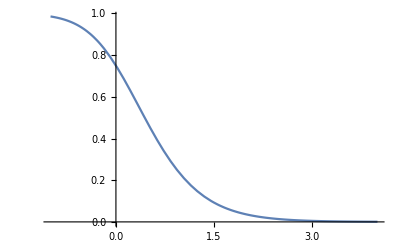

```mathematica
Module[
{ν0,k,β,ζ},
ν0=0;
k=1;
β=2;
ζ=.5;
Plot[fGLogistic[ν,ν0,k,β,ζ],{ν,-1,4}]
]
```

#### Fixed Homeostasis

Find ν where f(ν) = 1:

```mathematica
Solve[fGLogistic[ν,ν0,k,β,ζ]==1,ν]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ν→ν0-Log[-1+((-1+k)/k)^-ζ]/β}}

Requirement for homeostasis: f(0)=1

```mathematica
Simplify[Reduce[fGLogistic[0,ν0,k,β,ζ]==1],Assumptions->{k>1,β>0,ζ>0}]
```

(1+ⅇ^(β ν0))^(1/ζ)==k/(-1+k)

```mathematica
Solve[(1+ⅇ^(β ν0))^(1/ζ)==k/(-1+k),ζ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ζ→Log[1+ⅇ^(β ν0)]/Log[-k/(1-k)]}}

Fixed ζ

```mathematica
Module[
{ζ},
Manipulate[
ζ=Log[1+ⅇ^(β ν0)]/Log[-k/(1-k)];
Plot[fGLogistic[ν,ν0,k,β,ζ],{ν,-1,4},PlotRange->{0,k}],

{{k,2},2,10},
{{β,1},1,200},
{{ν0,0},0,10}
]
]
```

Fixed ν0

```mathematica
Solve[(1+ⅇ^(β ν0))^(1/ζ)==k/(-1+k),ν0]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ν0→Log[-1+(-k/(1-k))^ζ]/β}}

```mathematica
Module[
{ν0},
Manipulate[
ν0=Log[-1+(-k/(1-k))^ζ]/β;
Plot[fGLogistic[ν,ν0,k,β,ζ],{ν,-1,1},PlotRange->{0,k}],

{{k,10},2,20},
{{β,9},1,20},
{{ζ,1},0.01,10}
]
]
```

```mathematica
vTLog1[ν_,j_,k_,β_]=
Module[
{ζ,ν0},
ζ=1;
ν0=Log[-1+(-k/(1-k))^ζ]/β;
Subscript[vH, j] *fGLogistic[ν,ν0,k,β,ζ]//Simplify
]

sTLog1[ν_,j_,k_,β_]=
Module[
{ζ,ν0},
ζ=1;
ν0=Log[-1+(-k/(1-k))^ζ]/β;
Subscript[sH, j] *fGLogistic[ν,ν0,k,β,ζ]//Simplify
]
```

(k vH_j)/(1+ⅇ^(β ν) (-1+k))

(k sH_j)/(1+ⅇ^(β ν) (-1+k))

```mathematica
Simplify[Reduce[{vTLog1[ν,j,kv,βv]-sTLog1[ν,j,ks,βs]==Subscript[vH, j]-Subscript[sH, j]}],Assumptions->{ks>1,kv>1,βs>1,βv>1,Subscript[vH, j]>0,Subscript[sH, j]>0}]
```

(-1+ⅇ^(βs ν)) (-1+ks) (1+ⅇ^(βv ν) (-1+kv)) sH_j==(-1+ⅇ^(βv ν)) (1+ⅇ^(βs ν) (-1+ks)) (-1+kv) vH_j&&(1+ⅇ^(βv ν) (-1+kv)) ((ks+ⅇ^(βv ν) (-1+ks) (-1+kv)-ⅇ^((βs+βv) ν) (-1+ks) (-1+kv)) sH_j+ⅇ^(βv ν) (1+ⅇ^(βs ν) (-1+ks)) (-1+kv) vH_j)≠0

```mathematica
Series[vTLog1[ν,j,kv,βv],{ν,0,2}]
```

vH_j-((-1+kv) βv vH_j ν)/kv+((2-3 kv+kv^2) βv^2 vH_j ν^2)/(2 kv^2)+O[ν]^3

## General system

```mathematica
deSystemGeneral[t_,nAmps_,cP_,nP_,κs_,κv_,αs_,αv_,κsHSC_,κvHSC_,αsHSC_,αvHSC_]:=
Module[
{},

Join[
{D[Subscript[ν, 0][t],t]==(vT[Subscript[ν, 1][t],0,κvHSC,αvHSC]-sT[Subscript[ν, 1][t],0,κsHSC,αsHSC])(1+Subscript[ν, 0][t])},
{D[Subscript[ν, 1][t],t]==2sT[Subscript[ν, 1][t],0,κsHSC,αsHSC](1+Subscript[ν, 0][t])2ϵ/η+ (vT[Subscript[ν, 2][t],1,κv,αv]-sT[Subscript[ν, 2][t],1,κs,αs])(1+Subscript[ν, 1][t])},
Array[
D[Subscript[ν, #][t],t]==2sT[Subscript[ν, #][t],#-1,κs,αs](1+Subscript[ν, #-1][t])/η+ (vT[Subscript[ν, #+1][t],#,κv,αv]-sT[Subscript[ν, #+1][t],#,κs,αs])(1+Subscript[ν, #][t])&,
nAmps-1,2
],
{D[Subscript[ν, nAmps+1][t],t]==sT[Subscript[ν, nAmps+1][t],nAmps,κs,αs](1+Subscript[ν, nAmps][t])μbs/Subscript[sH, nAmps]-(μbs)(1+Subscript[ν, nAmps+1][t])},

Array[
Which[#==cP,Subscript[ν, cP][0]==nP,#≠cP,Subscript[ν, #][0]==0]&,
nAmps+2,0
]
]/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]}
]
deSystemGeneral[t_,nAmps_,cP_,nP_,κs_,κv_,αs_,αv_,κsHSC_,κvHSC_,αsHSC_,αvHSC_,ϕ_]:=
Module[
{},

Join[
{D[Subscript[ν, 0][t],t]==(vT[Subscript[ν, 1][t],0,κvHSC,αvHSC]-sT[Subscript[ν, 1][t],0,κsHSC,αsHSC])(1+Subscript[ν, 0][t])},
{D[Subscript[ν, 1][t],t]==2sT[Subscript[ν, 1][t],0,κsHSC,αsHSC](1+Subscript[ν, 0][t])2ϵ/η+ (vT[Subscript[ν, 2][t],1,κv,αv]-sT[Subscript[ν, 2][t],1,κs,αs])(1+Subscript[ν, 1][t])},
Array[
D[Subscript[ν, #][t],t]==2sT[Subscript[ν, #][t],#-1,κs,αs](1+Subscript[ν, #-1][t])/η+ (vT[Subscript[ν, #+1][t],#,κv,αv]-sT[Subscript[ν, #+1][t],#,κs,αs])(1+Subscript[ν, #][t])&,
nAmps-1,2
],
{D[Subscript[ν, nAmps+1][t],t]==sT[Subscript[ν, nAmps+1][t],nAmps,κs,αs](1+Subscript[ν, nAmps][t])μbs/Subscript[sH, nAmps]-(μbs+ϕ)(1+Subscript[ν, nAmps+1][t])},

Array[
Which[#==cP,Subscript[ν, cP][0]==nP,#≠cP,Subscript[ν, #][0]==0]&,
nAmps+2,0
]
]/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]}
]
TableForm[deSystemGeneral[t,5,6,-0.2,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]]
```

ν_0'[t]==(-sT[ν_1[t],0,κsHSC,αsHSC]+vT[ν_1[t],0,κvHSC,αvHSC]) (1+ν_0[t])
ν_1'[t]==(4 ϵ sT[ν_1[t],0,κsHSC,αsHSC] (1+ν_0[t]))/η+(-sT[ν_2[t],1,κs,αs]+vT[ν_2[t],1,κv,αv]) (1+ν_1[t])
ν_2'[t]==(2 sT[ν_2[t],1,κs,αs] (1+ν_1[t]))/η+(-sT[ν_3[t],2,κs,αs]+vT[ν_3[t],2,κv,αv]) (1+ν_2[t])
ν_3'[t]==(2 sT[ν_3[t],2,κs,αs] (1+ν_2[t]))/η+(-sT[ν_4[t],3,κs,αs]+vT[ν_4[t],3,κv,αv]) (1+ν_3[t])
ν_4'[t]==(2 sT[ν_4[t],3,κs,αs] (1+ν_3[t]))/η+(-sT[ν_5[t],4,κs,αs]+vT[ν_5[t],4,κv,αv]) (1+ν_4[t])
ν_5'[t]==(2 sT[ν_5[t],4,κs,αs] (1+ν_4[t]))/η+(-sT[ν_bs[t],5,κs,αs]+vT[ν_bs[t],5,κv,αv]) (1+ν_5[t])
ν_bs'[t]==(μbs sT[ν_bs[t],5,κs,αs] (1+ν_5[t]))/sH_5-(μbs+ϕ) (1+ν_bs[t])
ν_0[0]==0
ν_1[0]==0
ν_2[0]==0
ν_3[0]==0
ν_4[0]==0
ν_5[0]==0
ν_bs[0]==-0.2

```mathematica
deSystem2General[t_,nAmps_,cP_,nP_,κs_,κv_,αs_,αv_,κsHSC_,κvHSC_,αsHSC_,αvHSC_,ϕ_]:=
Module[
{},

Join[
{D[Subscript[ν, 0][t],t]==(vT[Subscript[ν, nAmps+1][t],0,κvHSC,αvHSC]-sT[Subscript[ν, nAmps+1][t],0,κsHSC,αsHSC])(1+Subscript[ν, 0][t])},
{D[Subscript[ν, 1][t],t]==2sT[Subscript[ν, nAmps+1][t],0,κsHSC,αsHSC](1+Subscript[ν, 0][t])2ϵ/η+ (vT[Subscript[ν, nAmps+1][t],1,κv,αv]-sT[Subscript[ν, nAmps+1][t],1,κs,αs])(1+Subscript[ν, 1][t])},
Array[
D[Subscript[ν, #][t],t]==2sT[Subscript[ν, nAmps+1][t],#-1,κs,αs](1+Subscript[ν, #-1][t])/η+ (vT[Subscript[ν, nAmps+1][t],#,κv,αv]-sT[Subscript[ν, nAmps+1][t],#,κs,αs])(1+Subscript[ν, #][t])&,
nAmps-1,2
],
{D[Subscript[ν, nAmps+1][t],t]==sT[Subscript[ν, nAmps+1][t],nAmps,κs,αs](1+Subscript[ν, nAmps][t])μbs/Subscript[sH, nAmps]-(μbs+ϕ)(1+Subscript[ν, nAmps+1][t])},

Array[
Which[#==cP,Subscript[ν, cP][0]==nP,#≠cP,Subscript[ν, #][0]==0]&,
nAmps+2,0
]
]/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]}
]
TableForm[deSystemGeneral[t,5,6,-0.2,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]]
TableForm[deSystem2General[t,5,6,-0.2,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]]
```

ν_0'[t]==(-sT[ν_1[t],0,κsHSC,αsHSC]+vT[ν_1[t],0,κvHSC,αvHSC]) (1+ν_0[t])
ν_1'[t]==(4 ϵ sT[ν_1[t],0,κsHSC,αsHSC] (1+ν_0[t]))/η+(-sT[ν_2[t],1,κs,αs]+vT[ν_2[t],1,κv,αv]) (1+ν_1[t])
ν_2'[t]==(2 sT[ν_2[t],1,κs,αs] (1+ν_1[t]))/η+(-sT[ν_3[t],2,κs,αs]+vT[ν_3[t],2,κv,αv]) (1+ν_2[t])
ν_3'[t]==(2 sT[ν_3[t],2,κs,αs] (1+ν_2[t]))/η+(-sT[ν_4[t],3,κs,αs]+vT[ν_4[t],3,κv,αv]) (1+ν_3[t])
ν_4'[t]==(2 sT[ν_4[t],3,κs,αs] (1+ν_3[t]))/η+(-sT[ν_5[t],4,κs,αs]+vT[ν_5[t],4,κv,αv]) (1+ν_4[t])
ν_5'[t]==(2 sT[ν_5[t],4,κs,αs] (1+ν_4[t]))/η+(-sT[ν_bs[t],5,κs,αs]+vT[ν_bs[t],5,κv,αv]) (1+ν_5[t])
ν_bs'[t]==(μbs sT[ν_bs[t],5,κs,αs] (1+ν_5[t]))/sH_5-(μbs+ϕ) (1+ν_bs[t])
ν_0[0]==0
ν_1[0]==0
ν_2[0]==0
ν_3[0]==0
ν_4[0]==0
ν_5[0]==0
ν_bs[0]==-0.2

ν_0'[t]==(-sT[ν_bs[t],0,κsHSC,αsHSC]+vT[ν_bs[t],0,κvHSC,αvHSC]) (1+ν_0[t])
ν_1'[t]==(4 ϵ sT[ν_bs[t],0,κsHSC,αsHSC] (1+ν_0[t]))/η+(-sT[ν_bs[t],1,κs,αs]+vT[ν_bs[t],1,κv,αv]) (1+ν_1[t])
ν_2'[t]==(2 sT[ν_bs[t],1,κs,αs] (1+ν_1[t]))/η+(-sT[ν_bs[t],2,κs,αs]+vT[ν_bs[t],2,κv,αv]) (1+ν_2[t])
ν_3'[t]==(2 sT[ν_bs[t],2,κs,αs] (1+ν_2[t]))/η+(-sT[ν_bs[t],3,κs,αs]+vT[ν_bs[t],3,κv,αv]) (1+ν_3[t])
ν_4'[t]==(2 sT[ν_bs[t],3,κs,αs] (1+ν_3[t]))/η+(-sT[ν_bs[t],4,κs,αs]+vT[ν_bs[t],4,κv,αv]) (1+ν_4[t])
ν_5'[t]==(2 sT[ν_bs[t],4,κs,αs] (1+ν_4[t]))/η+(-sT[ν_bs[t],5,κs,αs]+vT[ν_bs[t],5,κv,αv]) (1+ν_5[t])
ν_bs'[t]==(μbs sT[ν_bs[t],5,κs,αs] (1+ν_5[t]))/sH_5-(μbs+ϕ) (1+ν_bs[t])
ν_0[0]==0
ν_1[0]==0
ν_2[0]==0
ν_3[0]==0
ν_4[0]==0
ν_5[0]==0
ν_bs[0]==-0.2

```mathematica
(*deSystemLin[t_,nAmps_,cP_,nP_,κs_,κv_,αs_,αv_,κsHSC_,κvHSC_,αsHSC_,αvHSC_]:=
deSystemGeneral[t,nAmps,cP,nP,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC]/.{sT->sTLin,vT->vTLin}/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]};*)
```

```mathematica
(*deSystemLinStep[t_,nAmps_,cP_,nP_,κs_,κv_,αs_,αv_,κsHSC_,κvHSC_,αsHSC_,αvHSC_]:=
deSystemGeneral[t,nAmps,cP,nP,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC]/.{sT->sTLinStep,vT->vTLinStep}/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]};*)

TableForm[deSystemGeneral[t,5,6,nP,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]/.{sT->sTLinStep,vT->vTLinStep};];
TableForm[deSystemGeneral[t,5,6,nP,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]/.{sT->sTLinStep,vT->vTLinStep}]/.ruleRatesToRρϵ;
TableForm[deSystemGeneral[t,5,6,nP,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]/.{sT->sTLinStep,vT->vTLinStep}]/.ruleRatesToRρϵ/.ruleϵηρToAmpsParams[5,ruleParams]/.ruleParams;
```

```mathematica
νVec[nAmps_]:=Join[Array[Subscript[ν, #]&,nAmps+1,0],{Subscript[ν, bs]}]
νVect[nAmps_,t_]:=νVec[nAmps]/.{Subscript[ν, j_]->Subscript[ν, j][t]}
(*νVec[5]
νVect[5,t]*)
```

```mathematica
epsilonNu[ν_,j_,κs_,κv_,αs_,αv_]:=sT[ν,j,κs,αs]/(sT[ν,j,κs,αs] + vT[ν,j,κv,αv]);
rRelNu[ν_,j_,κs_,κv_,αs_,αv_]:=(sT[ν,j,κs,αs] + vT[ν,j,κv,αv])/(Subscript[sH, j]+Subscript[vH, j]);
epsilonNu[ν,j,κs,κv,αs,αv]
rRelNu[ν,j,κs,κv,αs,αv]
```

sT[ν,j,κs,αs]/(sT[ν,j,κs,αs]+vT[ν,j,κv,αv])

(sT[ν,j,κs,αs]+vT[ν,j,κv,αv])/(sH_j+vH_j)

### Chronic Perturbations

```mathematica
deSystemGeneral[t_,nAmps_,cP_,nP_,κs_,κv_,αs_,αv_,κsHSC_,κvHSC_,αsHSC_,αvHSC_,p_,μPNH_]:=
Module[
{},

Join[
{D[Subscript[ν, 0][t],t]==(vT[Subscript[ν, 1][t],0,κvHSC,αvHSC]-sT[Subscript[ν, 1][t],0,κsHSC,αsHSC])(1+Subscript[ν, 0][t])},
{D[Subscript[ν, 1][t],t]==2sT[Subscript[ν, 1][t],0,κsHSC,αsHSC](1+Subscript[ν, 0][t])2ϵ/η+ (vT[Subscript[ν, 2][t],1,κv,αv]-sT[Subscript[ν, 2][t],1,κs,αs])(1+Subscript[ν, 1][t])},
Array[
D[Subscript[ν, #][t],t]==2sT[Subscript[ν, #][t],#-1,κs,αs](1+Subscript[ν, #-1][t])/η+ (vT[Subscript[ν, #+1][t],#,κv,αv]-sT[Subscript[ν, #+1][t],#,κs,αs])(1+Subscript[ν, #][t])&,
nAmps-1,2
],
{D[nNorm[t],t]==2sT[Subscript[ν, nAmps+1][t],nAmps,κs,αs] Subscript[nH, nAmps](1+Subscript[ν, nAmps][t])(1-p)-μbs nNorm[t]},
{D[nPNH[t],t]==2sT[Subscript[ν, nAmps+1][t],nAmps,κs,αs] Subscript[nH, nAmps](1+Subscript[ν, nAmps][t])p-μPNH nPNH[t]},
{Subscript[ν, nAmps+1][t]==(nNorm[t]+nPNH[t]-nHbs)/nHbs},
Array[
Which[#==cP,Subscript[ν, cP][0]==nP,#≠cP,Subscript[ν, #][0]==0]&,
nAmps+1,0
],
{nNorm[0]==(1-p)*nHbs},
{nPNH[0]==p*nHbs},
{Subscript[ν, bs][0]==0}
]/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]}/.ruleCompsizeBloodToAmps[nAmps]
]
TableForm[deSystemGeneral[t,5,6,0,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,p, μPNH]]
TableForm[deSystemGeneral[t,5,6,0,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,p, μPNH]]/.ruleCompsizesToηϵ
```

ν_0'[t]==(-sT[ν_1[t],0,κsHSC,αsHSC]+vT[ν_1[t],0,κvHSC,αvHSC]) (1+ν_0[t])
ν_1'[t]==(4 ϵ sT[ν_1[t],0,κsHSC,αsHSC] (1+ν_0[t]))/η+(-sT[ν_2[t],1,κs,αs]+vT[ν_2[t],1,κv,αv]) (1+ν_1[t])
ν_2'[t]==(2 sT[ν_2[t],1,κs,αs] (1+ν_1[t]))/η+(-sT[ν_3[t],2,κs,αs]+vT[ν_3[t],2,κv,αv]) (1+ν_2[t])
ν_3'[t]==(2 sT[ν_3[t],2,κs,αs] (1+ν_2[t]))/η+(-sT[ν_4[t],3,κs,αs]+vT[ν_4[t],3,κv,αv]) (1+ν_3[t])
ν_4'[t]==(2 sT[ν_4[t],3,κs,αs] (1+ν_3[t]))/η+(-sT[ν_5[t],4,κs,αs]+vT[ν_5[t],4,κv,αv]) (1+ν_4[t])
ν_5'[t]==(2 sT[ν_5[t],4,κs,αs] (1+ν_4[t]))/η+(-sT[ν_bs[t],5,κs,αs]+vT[ν_bs[t],5,κv,αv]) (1+ν_5[t])
nNorm'[t]==-μbs nNorm[t]+2 (1-p) sT[ν_bs[t],5,κs,αs] nH_5 (1+ν_5[t])
nPNH'[t]==-μPNH nPNH[t]+2 p sT[ν_bs[t],5,κs,αs] nH_5 (1+ν_5[t])
ν_bs[t]==(μbs (nNorm[t]+nPNH[t]-(2 nH_5 sH_5)/μbs))/(2 nH_5 sH_5)
ν_0[0]==0
ν_1[0]==0
ν_2[0]==0
ν_3[0]==0
ν_4[0]==0
ν_5[0]==0
nNorm[0]==(2 (1-p) nH_5 sH_5)/μbs
nPNH[0]==(2 p nH_5 sH_5)/μbs
ν_bs[0]==0

ν_0'[t]==(-sT[ν_1[t],0,κsHSC,αsHSC]+vT[ν_1[t],0,κvHSC,αvHSC]) (1+ν_0[t])
ν_1'[t]==(4 ϵ sT[ν_1[t],0,κsHSC,αsHSC] (1+ν_0[t]))/η+(-sT[ν_2[t],1,κs,αs]+vT[ν_2[t],1,κv,αv]) (1+ν_1[t])
ν_2'[t]==(2 sT[ν_2[t],1,κs,αs] (1+ν_1[t]))/η+(-sT[ν_3[t],2,κs,αs]+vT[ν_3[t],2,κv,αv]) (1+ν_2[t])
ν_3'[t]==(2 sT[ν_3[t],2,κs,αs] (1+ν_2[t]))/η+(-sT[ν_4[t],3,κs,αs]+vT[ν_4[t],3,κv,αv]) (1+ν_3[t])
ν_4'[t]==(2 sT[ν_4[t],3,κs,αs] (1+ν_3[t]))/η+(-sT[ν_5[t],4,κs,αs]+vT[ν_5[t],4,κv,αv]) (1+ν_4[t])
ν_5'[t]==(2 sT[ν_5[t],4,κs,αs] (1+ν_4[t]))/η+(-sT[ν_bs[t],5,κs,αs]+vT[ν_bs[t],5,κv,αv]) (1+ν_5[t])
nNorm'[t]==-μbs nNorm[t]+(nHSC (1-p) η^5 sT[ν_bs[t],5,κs,αs] (1+ν_5[t]))/ϵ
nPNH'[t]==-μPNH nPNH[t]+(nHSC p η^5 sT[ν_bs[t],5,κs,αs] (1+ν_5[t]))/ϵ
ν_bs[t]==(ϵ μbs (nNorm[t]+nPNH[t]-(nHSC η^5 sH_5)/(ϵ μbs)))/(nHSC η^5 sH_5)
ν_0[0]==0
ν_1[0]==0
ν_2[0]==0
ν_3[0]==0
ν_4[0]==0
ν_5[0]==0
nNorm[0]==(nHSC (1-p) η^5 sH_5)/(ϵ μbs)
nPNH[0]==(nHSC p η^5 sH_5)/(ϵ μbs)
ν_bs[0]==0

```mathematica
nHbs/.ruleCompsizeBloodToAmps[4]
```

(2 nH_4 sH_4)/μbs

### Logistic System

```mathematica
ruleϵηρToAmpsParams[5,ruleParams]
```

{nHk→6.96499×10^10,ϵ→0.502514,η→44.5254,ρ→4.49006}

```mathematica
(*deSystemLog[t_,nAmps_,cP_,nP_,κs_,κv_,αs_,αv_,κsHSC_,κvHSC_,αsHSC_,αvHSC_]:=
deSystemGeneral[t,nAmps,cP,nP,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC]/.{sT->sTLog1,vT->vTLog1}/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]};*)
TableForm[deSystemGeneral[t,5,6,-0.2,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]];
TableForm[deSystemGeneral[t,5,6,-0.2,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]/.{sT->sTLog1,vT->vTLog1}];
TableForm[deSystemGeneral[t,5,6,-0.2,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]/.{sT->sTLog1,vT->vTLog1}]/.ruleRatesToRρϵ/.ruleϵηρToAmpsParams[5,ruleParams]/.ruleParams;
TableForm[deSystemGeneral[t,5,6,-0.2,5,5,10,10,5,5,1,1]/.{sT->sTLog1,vT->vTLog1}]/.ruleRatesToRρϵ/.ruleϵηρToAmpsParams[5,ruleParams]/.ruleParams;
TableForm[deSystemGeneral[t,10,11,0,4,4,7,5,10,10,10,10,0.5,0.2]]/.ruleCompsizeBloodToAmps[10]/.ruleCompsizesToηϵ/.{sT->sTLog1,vT->vTLog1}/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]}/.ruleRatesToRρϵ/.ruleϵηρToAmpsParams[10,ruleParams]/.ruleParams;
deSystemGeneral[t,5,11,0,4,4,7,5,10,10,10,10,0.5,0.2]/.ruleCompsizeBloodToAmps[5]/.ruleCompsizesToηϵ/.{sT->sTLog1,vT->vTLog1}/.ruleRatesToRρϵ/.ruleϵηρToAmpsParams[5,ruleParams]/.ruleParams
```

{ν_0'[t]==0,ν_1'[t]==(0.000618411 (1+ν_0[t]))/(1+9 ⅇ^(10 ν_1[t]))+(0.0244794/(1+3 ⅇ^(5 ν_2[t]))-0.0247268/(1+3 ⅇ^(7 ν_2[t]))) (1+ν_1[t]),ν_2'[t]==(0.00111068 (1+ν_1[t]))/(1+3 ⅇ^(7 ν_2[t]))+(0.109914/(1+3 ⅇ^(5 ν_3[t]))-0.111025/(1+3 ⅇ^(7 ν_3[t]))) (1+ν_2[t]),ν_3'[t]==(0.00498704 (1+ν_2[t]))/(1+3 ⅇ^(7 ν_3[t]))+(0.493522/(1+3 ⅇ^(5 ν_4[t]))-0.498509/(1+3 ⅇ^(7 ν_4[t]))) (1+ν_3[t]),ν_4'[t]==(0.0223921 (1+ν_3[t]))/(1+3 ⅇ^(7 ν_4[t]))+(2.21594/(1+3 ⅇ^(5 ν_5[t]))-2.23834/(1+3 ⅇ^(7 ν_5[t]))) (1+ν_4[t]),ν_5'[t]==(0.100542 (1+ν_4[t]))/(1+3 ⅇ^(7 ν_5[t]))+(9.94973/(1+3 ⅇ^(5 ν_bs[t]))-10.0503/(1+3 ⅇ^(7 ν_bs[t]))) (1+ν_5[t]),nNorm'[t]==-nNorm[t]/100+(7.×10^11 (1+ν_5[t]))/(1+3 ⅇ^(7 ν_bs[t])),nPNH'[t]==-0.2 nPNH[t]+(7.×10^11 (1+ν_5[t]))/(1+3 ⅇ^(7 ν_bs[t])),ν_bs[t]==2.85714×10^-14 (-3.5×10^13+nNorm[t]+nPNH[t]),ν_0[0]==0,ν_1[0]==0,ν_2[0]==0,ν_3[0]==0,ν_4[0]==0,ν_5[0]==0,nNorm[0]==1.75×10^13,nPNH[0]==1.75×10^13,ν_bs[0]==0}

```mathematica
With[{nAmps=5},
NDSolve[
deSystemGeneral[t,nAmps,nAmps+1,0,4,4,7,5,10,10,10,10,0.8,0.2]/.ruleCompsizeBloodToAmps[nAmps]/.ruleCompsizesToηϵ/.{sT->sTLog1,vT->vTLog1}/.ruleRatesToRρϵ/.ruleϵηρToAmpsParams[nAmps,ruleParams]/.ruleParams,
νVec[nAmps],
{t,0,100}]
]
```

{{ν_0→InterpolatingFunction[…],ν_1→InterpolatingFunction[…],ν_2→InterpolatingFunction[…],ν_3→InterpolatingFunction[…],ν_4→InterpolatingFunction[…],ν_5→InterpolatingFunction[…],ν_bs→InterpolatingFunction[…]}}

## Solutions

## Small Compartment number

## Sequential

```mathematica
Module[
{legends,ruleParams1,compPerturb,plotComps,plotRange,ϵνT,rνT,vTType,sTType,sRelT,vRelT,svFrac,αv,κs,κv},

vTType=vTLog1;
sTType=sTLog1;
ϵνT[ν_,j_,κs_,κv_,αs_,αv_]:=epsilonNu[ν,j,κs,κv,αs,αv]/.{vT-> vTType,sT->sTType};
rνT[ν_,j_,κs_,κv_,αs_,αv_]:=rRelNu[ν,j,κs,κv,αs,αv]/.{vT-> vTType,sT->sTType};
sRelT[ν_,j_,κs_,αs_]:=sTType[ν,j,κs,αs]/Subscript[sH, j];
vRelT[ν_,j_,κv_,αv_]:=vTType[ν,j,κv,αv]/Subscript[vH, j];

Manipulate[
compPerturb=nAmps+1;

plotComps={nAmps+1,nAmps,nAmps-1,nAmps-2,1,0};
ruleParams1=Join[ruleϵηρToAmpsParams[nAmps,ruleParams],ruleParams];
legends[nAmps_]:=Join[Array[ToString[Subscript[ν, #],FormatType->StandardForm]&,nAmps+1,0],{"ν_BS"}];

svFrac=Subscript[sH, 1]/Subscript[vH, 1]/.ruleRatesToRρϵ/.ruleParams/.ruleParams1;
αv=αs*svFrac+dαv;
αvHSC=αsHSC+dαvHSC;
κs=κ;
κv=κ;

plotRange={νMin*10^(-1),νMax*10^(-1)};

sol=
NDSolve[
deSystemGeneral[t,nAmps,compPerturb,initialPerturb,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,ϕ]
/.{sT->sTType,vT->vTType}/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]}/.ruleRatesToRρϵ/.ruleParams1,νVec[nAmps],
{t,0,timeStop}];

Grid[
{

 {Plot[Evaluate[(Evaluate[νVect[nAmps,t]/.sol])[[1]]  [[plotComps+1]]  ],
{t,0,timeStop},
AxesLabel->{"t (days)", ν},
TicksStyle->Directive[Black,15],
PlotRange-> plotRange,
PlotLegends->Placed[{legends[nAmps][[plotComps+1]]},{Right,Right}],
PlotStyle-> Automatic,
ImageSize-> {500,300}]},


{Grid[
{{
Plot[
Evaluate[
Prepend[sRelT[Subscript[ν, #+1][t],#,Which[#>0,κs,#==0,κsHSC],Which[#>0,αs,#==0,αsHSC]]&/@plotComps[[2;;-1]],nothing]/.{Subscript[ν, nAmps+1]->Subscript[ν, bs]}/.sol/.ruleRatesToRρϵ/.ruleParams1],
{t,0,timeStop},PlotRange-> {0,5},AxesLabel->{"t (days)", "s_j(t)"}],
Plot[
Evaluate[
Prepend[vRelT[Subscript[ν, #+1][t],#,Which[#>0,κv,#==0,κvHSC],Which[#>0,αv,#==0,αvHSC]]&/@plotComps[[2;;-1]],nothing]/.{Subscript[ν, nAmps+1]->Subscript[ν, bs]}/.sol/.ruleRatesToRρϵ/.ruleParams1],
{t,0,timeStop},PlotRange-> {0,5},AxesLabel->{"t (days)", "v_j(t)"}]
}}
]},

{
Plot[
Evaluate[
Prepend[
sTType[Subscript[ν, #+1][t],#,Which[#>0,κs,#==0,κsHSC],Which[#>0,αs,#==0,αsHSC]]/(sTType[Subscript[ν, #+1][t],#,Which[#>0,κs,#==0,κsHSC],Which[#>0,αs,#==0,αsHSC]]+vTType[Subscript[ν, #+1][t],#,Which[#>0,κv,#==0,κvHSC],Which[#>0,αv,#==0,αvHSC]])
(*ϵνT[Subscript[ν, #+1][t],#,Which[#>0,κs,#==0,κsHSC],Which[#>0,κv,#==0,κvHSC],Which[#>0,αs,#==0,αsHSC],Which[#>0,αs,#==0,αsHSC]]*)
&/@plotComps[[2;;-1]],nothing]/.{Subscript[ν, nAmps+1]->Subscript[ν, bs]}/.sol/.ruleRatesToRρϵ/.ruleParams1],
{t,0,timeStop},PlotRange-> {0.5,0.6},AxesLabel->{"t (days)", "ϵ_j(t)"}]
}
},
Alignment-> Center],
{{nAmps,10},2,15,1,Appearance-> "Labeled"},
{{initialPerturb,-0.2},0,-0.9,Appearance-> "Labeled"},
{{ϕ,0},-0.1,0.1,Appearance->"Labeled"},
{{κ,3.6},2,100,Appearance-> "Labeled"},
{{αs,8},0,15,Appearance-> "Labeled"},
{{dαv,0},-0.5,0.5,Appearance->"labeled"},
(*{{αv,0},0,5,Appearance-> "Labeled"},*)
(*{{αv,αs*svFrac},0,30,Appearance-> "Labeled"},*)
{{κsHSC,500},2,500,Appearance-> "Labeled"},
{{κvHSC,500},2,500,Appearance-> "Labeled"},
{{αsHSC,0},0,50,Appearance-> "Labeled"},
{{dαvHSC,0},-2,2,Appearance-> "Labeled"},
{{νMin,-2},-10,-0.1},
{{νMax,2},0.1,60},
{{timeStop,350},2,5000}]


]
```

## Chronic perturbations

```mathematica
Module[
{legends,ruleParams1,compPerturb,plotComps,plotRange,ϵνT,rνT,vTType,sTType,sRelT,vRelT,svFrac,αv,κs,κv,αvHSC},

vTType=vTLog1;
sTType=sTLog1;
ϵνT[ν_,j_,κs_,κv_,αs_,αv_]:=epsilonNu[ν,j,κs,κv,αs,αv]/.{vT-> vTType,sT->sTType};
rνT[ν_,j_,κs_,κv_,αs_,αv_]:=rRelNu[ν,j,κs,κv,αs,αv]/.{vT-> vTType,sT->sTType};
sRelT[ν_,j_,κs_,αs_]:=sTType[ν,j,κs,αs]/Subscript[sH, j];
vRelT[ν_,j_,κv_,αv_]:=vTType[ν,j,κv,αv]/Subscript[vH, j];

Manipulate[
compPerturb=nAmps+1;

plotComps={nAmps+1,nAmps,nAmps-1,nAmps-2,1,0};
ruleParams1=Join[ruleϵηρToAmpsParams[nAmps,ruleParams],ruleParams];
legends[nAmps_]:=Join[Array[ToString[Subscript[ν, #],FormatType->StandardForm]&,nAmps+1,0],{"ν_BS"}];

svFrac=Subscript[sH, 1]/Subscript[vH, 1]/.ruleRatesToRρϵ/.ruleParams/.ruleParams1;
αv=αs*svFrac+dαv;
αvHSC=αsHSC+dαvHSC;
κs=κ;
κv=κ;

plotRange={νMin*10^(-1),νMax*10^(-1)};

sol=
NDSolve[
deSystemGeneral[t,nAmps,compPerturb,initialPerturb,κs,κv,αs,αv,κsHSC,κvHSC,αsHSC,αvHSC,p,μPNH]/.ruleCompsizeBloodToAmps[nAmps]/.ruleCompsizesToηϵ/.{sT->sTType,vT->vTType}/.{Subscript[ν, nAmps+1]-> Subscript[ν, bs]}/.ruleRatesToRρϵ/.ruleParams1,
νVec[nAmps],
{t,0,timeStop}];

Grid[
{

 {Plot[Evaluate[(Evaluate[νVect[nAmps,t]/.sol])[[1]]  [[plotComps+1]]  ],
{t,0,timeStop},
AxesLabel->{"t (days)", ν},
TicksStyle->Directive[Black,15],
PlotRange-> plotRange,
PlotLegends->Placed[{legends[nAmps][[plotComps+1]]},{Right,Right}],
PlotStyle-> Automatic,
ImageSize-> {500,300}]},


{Grid[
{{
Plot[
Evaluate[
Prepend[sRelT[Subscript[ν, #+1][t],#,Which[#>0,κs,#==0,κsHSC],Which[#>0,αs,#==0,αsHSC]]&/@plotComps[[2;;-1]],nothing]/.{Subscript[ν, nAmps+1]->Subscript[ν, bs]}/.sol/.ruleRatesToRρϵ/.ruleParams1],
{t,0,timeStop},PlotRange-> {0,5},AxesLabel->{"t (days)", "s_j(t)"}],
Plot[
Evaluate[
Prepend[vRelT[Subscript[ν, #+1][t],#,Which[#>0,κv,#==0,κvHSC],Which[#>0,αv,#==0,αvHSC]]&/@plotComps[[2;;-1]],nothing]/.{Subscript[ν, nAmps+1]->Subscript[ν, bs]}/.sol/.ruleRatesToRρϵ/.ruleParams1],
{t,0,timeStop},PlotRange-> {0,5},AxesLabel->{"t (days)", "v_j(t)"}]
}}
]},

{Grid[
{{"First order difference:",-αv Subscript[vH, 1]+αs Subscript[sH, 1]/.ruleRatesToRρϵ/.ruleParams1}}
]}

},
Alignment-> Center],
{{nAmps,5},2,10,1,Appearance-> "Labeled"},
{{initialPerturb,0},0,-0.9,Appearance-> "Labeled"},
{{p,0.8},0.05,0.95,Appearance->"Labeled"},
{{μPNH,0.2},0.01,1,Appearance->"Labeled"},
{{κ,7},2,15,Appearance-> "Labeled"},
{{αs,3.74},0,15,Appearance-> "Labeled"},
{{dαv,0.0635},-0.2,0.2,Appearance->"labeled"},
(*{{αv,0},0,5,Appearance-> "Labeled"},*)
(*{{αv,αs*svFrac},0,30,Appearance-> "Labeled"},*)
{{κsHSC,500},2,500,Appearance-> "Labeled"},
{{κvHSC,500},2,500,Appearance-> "Labeled"},
{{αsHSC,0},0,50,Appearance-> "Labeled"},
{{dαvHSC,0},-2,2,Appearance-> "Labeled"},
{{νMin,-4},-10,-0.1},
{{νMax,4},0.1,60},
{{timeStop,1000},2,5000}]


]
```